```mathematica
ClearAll["Global`*"]
```

## Transform uL using Irreps of H64

```mathematica
(*—1. Load H64 data—*)
SetDirectory[NotebookDirectory[]];
<<HopfAlgebraTools`;<<RMatTools`;<<TensorTool`;
H64Data=LoadHA["H64"];
mul=H64Data[[1]];
(*mul is your 64×4096 sparse array of structure constants*)
```

```mathematica
(*Import the tensors uL,uR,vL,vR from data file, each one is given as a m dA * m dA matrix. *){uL,uR,vL,vR}=Import["uvTensor.mx"];
```

```mathematica
(*—2. Form left-and right-multiplication blocks—*)
leftMats=Table[mul[[All,(i-1)*64+1;;i*64]],{i,1,64}];
rightMats=Table[mul[[All,i;;4096;;64]],{i,1,64}];
(*each entry of rightMats[[j]] is the 64×64 matrix "right-multiply by basis_j"*)
```

```mathematica
(*—3. Pick a random commutant element—*)
(*Hermitian commutant element:*)
weights=RandomReal[{-1,1},64];
Xgen=Sum[weights[[i]]*(rightMats[[i]]+ConjugateTranspose[rightMats[[i]]]),{i,1,64}];
(*Xgen is numeric,and by construction commutes with every leftMats[[i]]*)
```

```mathematica
(*Check hermicity*)
Xgen.ConjugateTranspose[Xgen]==ConjugateTranspose[Xgen].Xgen
```

True

```mathematica
(*—4. Diagonalize& orthonormalize->Ureg—*)
{vals,vecs}=Eigensystem[Xgen];
Ureg=Transpose[Orthogonalize[vecs]];
(*Sanity check:Norm[Ureg.ConjugateTranspose[Ureg]-IdentityMatrix[64]]~0*)
```

```mathematica
Norm[ConjugateTranspose[Ureg].Ureg]-Norm[IdentityMatrix[64]]
Chop[Ureg.ConjugateTranspose[Ureg],10^-15]==IdentityMatrix[64]
```

8.88178×10^-16

True

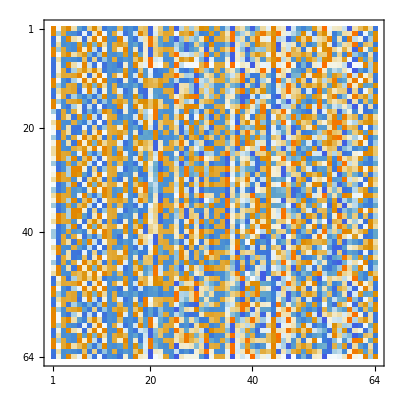

```mathematica
MatrixPlot[Chop[Ureg,10^-7]]
```

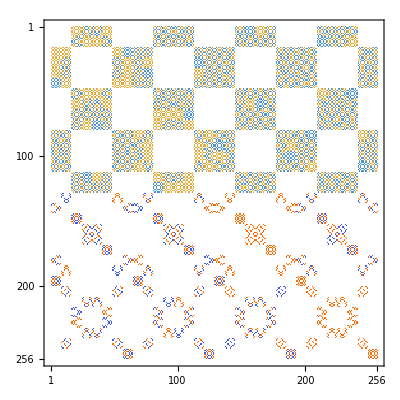

```mathematica
MatrixPlot[uL]
```

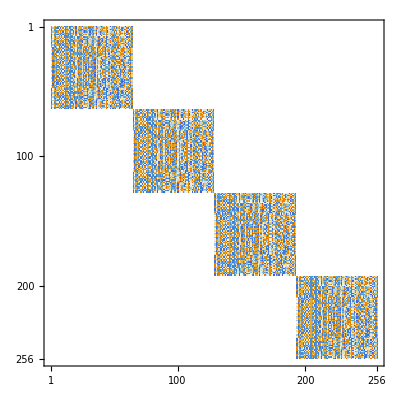

```mathematica
MatrixPlot[KroneckerProduct[IdentityMatrix[4],Ureg]]
```

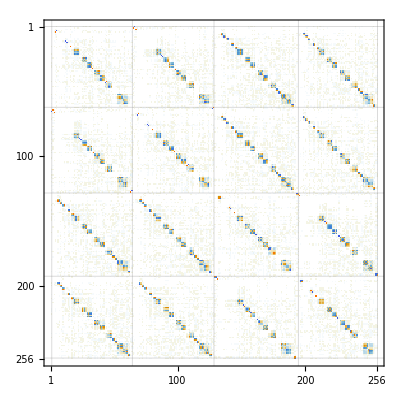

```mathematica
uLafter=ConjugateTranspose[KroneckerProduct[IdentityMatrix[4],Ureg]].uL.KroneckerProduct[IdentityMatrix[4],Ureg];
MatrixPlot[uLafter,GridLines->{{1,64,128,194,256}, {1,64,128,194,256}}]
```

```mathematica
Chop[ConjugateTranspose[uLafter].uLafter,10^-15]==IdentityMatrix[256]
```

True

```mathematica
Chop[uLafter.ConjugateTranspose[uLafter],10^-15]==IdentityMatrix[256]
```

True

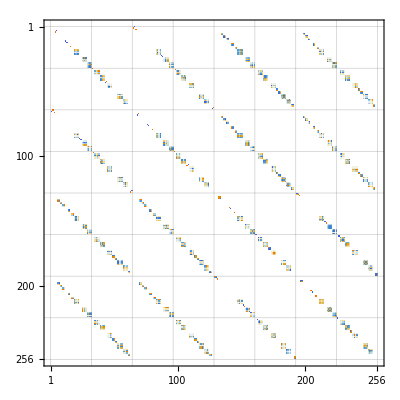

```mathematica
MatrixPlot[Chop[uLafter,10^-12],GridLines->{{0,32,64,96,128,160,192,224,256}, {0,32,64,96,128,160,192,224,256}}]
```

## Block diagonalize uLafter

```mathematica
perm={1,3,5,7,2,4,6,8};
S=IdentityMatrix[8][[perm,All]];
```

```mathematica
perm={1,2,5,6,3,4,7,8};
P=IdentityMatrix[8][[perm,All]];
```

As of now, we have found two unitary transformations that transform an 8x8 matrix with similar structure of uLafter into block diagonal form. We now apply these two basis transformations P and S to uLafter.

```mathematica
(*Define basis unitaries*)
(*We need 7 fold? I think*)
P1 = KroneckerProduct[P,IdentityMatrix[32]];
S1 = KroneckerProduct[S,IdentityMatrix[32]];
P2 = KroneckerProduct[IdentityMatrix[2],KroneckerProduct[P,IdentityMatrix[16]]];
S2 = KroneckerProduct[IdentityMatrix[2],KroneckerProduct[S,IdentityMatrix[16]]];
P3 = KroneckerProduct[IdentityMatrix[2],KroneckerProduct[IdentityMatrix[2],KroneckerProduct[P,IdentityMatrix[8]]]];
S3 = KroneckerProduct[IdentityMatrix[2],KroneckerProduct[IdentityMatrix[2],KroneckerProduct[S,IdentityMatrix[8]]]];
```

```mathematica
A = Chop[ConjugateTranspose[P2].ConjugateTranspose[S2].ConjugateTranspose[P1].ConjugateTranspose[S1].uLafter.S1.P1.S2.P2,10^-12];
```

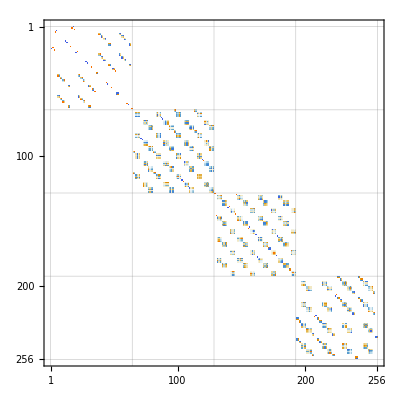

```mathematica
MatrixPlot[A,GridLines->{Table[64i,{i,0,4}],Table[64i,{i,0,4}]}]
```

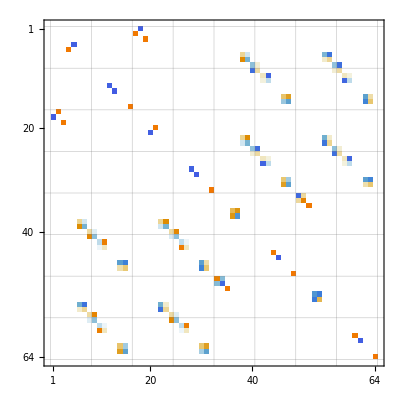

```mathematica
MatrixPlot[A[[1;;64,1;;64]],GridLines->{Table[8i,{i,0,8}],Table[8i,{i,0,8}]}]
```

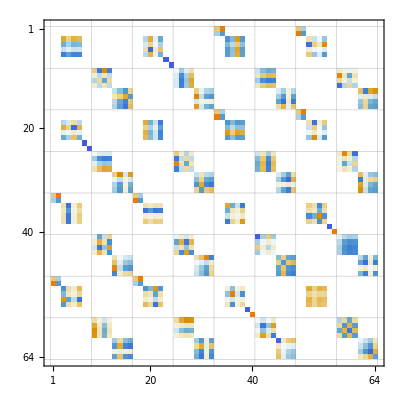

```mathematica
MatrixPlot[A[[65;;128,65;;128]],GridLines->{Table[8i,{i,0,8}],Table[8i,{i,0,8}]}]
```

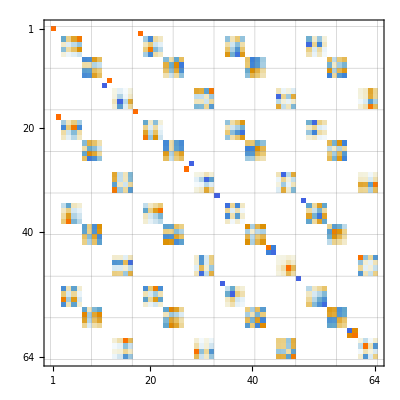

```mathematica
MatrixPlot[A[[129;;192,129;;192]],GridLines->{Table[8i,{i,0,8}],Table[8i,{i,0,8}]}]
```

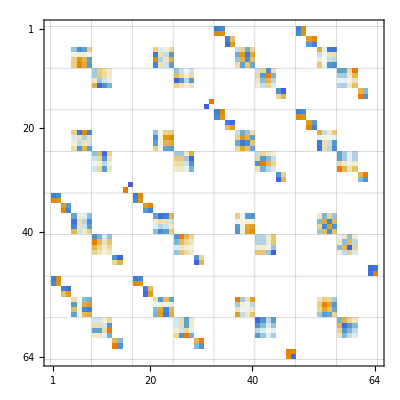

```mathematica
MatrixPlot[A[[193;;256,193;;256]],GridLines->{Table[8i,{i,0,8}],Table[8i,{i,0,8}]}]
```

```mathematica
Table[64i,{i,0,4}]
```

{0,64,128,192,256}

```mathematica
(*1) reshape S into a 4×64×4×64 tensor*)
sTensor=ArrayReshape[Chop[Ureg,10^-10],{4,64,4,64}];

(*2) extract two “factor-candidates”:
–pick block {a=1,b=1} to get S_phys–pick slice {α=1,β=1} to get S_anc*)
Sphys=sTensor[[1,All,1,All]];    (*64×64 matrix*)
Sanc=sTensor[[All,1,All,1]];    (*4×4 matrix*)

(*3) reconstruct the product*)
reconstructed=Table[Sanc[[a,b]]*Sphys[[α,β]],{a,4},{α,64},{b,4},{β,64}];

(*4) compare*)
If[Max[Abs[sTensor-reconstructed]]<10^-10,Print["✅ S factorizes: no ancilla–physical mixing."],Print["❌ S entangles ancilla & physical."]]
```

❌ S entangles ancilla & physical.